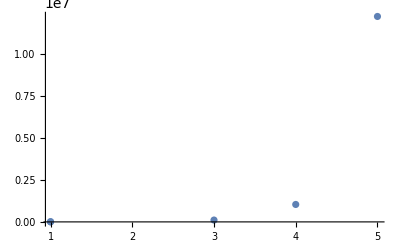

```mathematica
ListPlot[{{1, 1000}, {1, 12000}, {3, 110000}, {4, 1037000}, {5, 12218000}}, PlotRange->All]
```

```mathematica
epsilon[x_] = a0 + a1 + E^x + a2 *E^(2*x)+a3*E^(3*x) + a4*E^(4*x)
```

a0+a1+ⅇ^x+a2 ⅇ^(2 x)+a3 ⅇ^(3 x)+a4 ⅇ^(4 x)

```mathematica
e0 = epsilon[1.]
```

2.71828+a0+a1+7.38906 a2+20.0855 a3+54.5982 a4

```mathematica
e1 = epsilon[2.]
```

7.38906+a0+a1+54.5982 a2+403.429 a3+2980.96 a4

```mathematica
e2 = epsilon[3.]
```

20.0855+a0+a1+403.429 a2+8103.08 a3+162755. a4

```mathematica
e3 = epsilon[4.]
```

54.5982+a0+a1+2980.96 a2+162755. a3+8.88611×10^6 a4

```mathematica
e4 = epsilon[5.]
```

148.413+a0+a1+22026.5 a2+3.26902×10^6 a3+4.85165×10^8 a4

```mathematica
m = Table[E^((i)*(j -1)), {i, 5}, {j, 5}]
```

{{1,ⅇ,ⅇ^2,ⅇ^3,ⅇ^4},{1,ⅇ^2,ⅇ^4,ⅇ^6,ⅇ^8},{1,ⅇ^3,ⅇ^6,ⅇ^9,ⅇ^12},{1,ⅇ^4,ⅇ^8,ⅇ^12,ⅇ^16},{1,ⅇ^5,ⅇ^10,ⅇ^15,ⅇ^20}}

```mathematica
v = {1000 , 12000, 110000, 1037000, 12228000}
```

{1000,12000,110000,1037000,12228000}

```mathematica
LinearSolve[m, v] // N
```

{105.951,-382.885,257.356,1.64709,0.00253872}

```mathematica
epsilonSolved[x_] = 105.951 - 382.885*E^x + 257.356*E^(2*x) + 1.64709*E^(3*x) + 0.00253872*E^(4*x)
```

105.951-382.885 ⅇ^x+257.356 ⅇ^(2 x)+1.64709 ⅇ^(3 x)+0.00253872 ⅇ^(4 x)

```mathematica
For[i = 1, i < 6, i++, Print [epsilonSolved[i]]]
```

1000.

12000.

110000.

1.037×10^6

1.2228×10^7